# Vector beam focusing simulation

### We compute the integrals given in Youngworth & Brown, and another with the added cos(2θ) term in the azimuthal integral. The u and v parameters used are as defined in Richards and Wolf.

Define parameters:

```mathematica
p=10;(*number of integration points*)
λ=1;(*wavelength*)
k=(2 π)/λ;(*wavenumber*)
NA=1.32;(*numerical aperture*)
n=1.518;(*refractive index*)
α=ArcSin[NA/n](*angular extent of aperture*)
min=-2;max=2;step = 100;(*transverse dimensions in wavelengths*)
zmin=-2;zmax=2;zstep=100;(*longitudinal dimensions in wavelengths*)
f=100000 λ;(*focal length*)
l0=1;(*peak field amplitude*)
A=(π f l0)/λ;(*constant before integration*)
β=1.5;(*ratio of pupil radius to beam waist AT ENTRANCE PUPIL*)
u[z_]:=k z Sin[α]^2;(*as defined in Richards & Wolf*)
v2d = Table[{k Sin[α] √(x^2+y^2),z},{x,Range[min λ,max λ,(max-min)/step λ]},{y,Range[min λ,max λ,(max-min)/step λ]},{z,Range[zmin λ,zmax λ,(zmax-zmin)/zstep λ]}];
v1d=Abs[Table[{k Sin[α] Range[min λ,max λ,(max-min)/step λ],z},{z,Range[zmin λ,zmax λ,(zmax-zmin)/zstep λ]}]]; (*array with {v,z} value of each physical position*)
apod[θ_]:=Exp[-β^2 (Sin[θ]/Sin[α])^2]BesselJ[1,2 β Sin[θ]/Sin[α]];(*apodization function*)
```

1.05432

```mathematica
Trapezoidal rule (1D)
```

```mathematica
RHO1d=Z1d=PHI1d=PHI1dcos=0*v1d;
RHO1d[[All,2]]=Z1d[[All,2]]=PHI1d[[All,2]]=PHI1dcos[[All,2]]=v1d[[All,2]];
For[i=1,i<p,i++,RHO1d[[All,1]]=RHO1d[[All,1]]+(√Cos[i α/p]*Sin[2 i α/p]*apod[i α/p]*BesselJ[1,v1d[[All,1]] Sin[i α/p]/Sin[α]] *Exp[I u[RHO1d[[All,2]]] Cos[i α/p]/Sin[α]^2]);
Z1d[[All,1]]=Z1d[[All,1]]+(√Cos[i α/p]*Sin[i α/p]^2*apod[i α/p]*BesselJ[0,v1d[[All,1]] Sin[i α/p]/Sin[α]]* Exp[I u[Z1d[[All,2]]] Cos[i α/p]/Sin[α]^2]);PHI1d[[All,1]]=PHI1d[[All,1]]+(√Cos[i α/p]* Sin[i α/p]*apod[i α/p]*BesselJ[1,v1d[[All,1]] Sin[i α/p]/Sin[α]]*Exp[I u[PHI1d[[All,2]]] Cos[i α/p]/Sin[α]^2]);
PHI1dcos[[All,1]]=PHI1dcos[[All,1]]+(√Cos[i α/p]* Sin[i α/p]*Cos[2 i α/p]*apod[i α/p]*BesselJ[1,v1d[[All,1]] Sin[i α/p]/Sin[α]]*Exp[I u[PHI1d[[All,2]]] Cos[i α/p]/Sin[α]^2])];
RHO1d[[All,1]]=A α/p(RHO1d[[All,1]]+0.5*(√Cos[α]*Sin[2 α]*apod[α]*BesselJ[1,v1d[[All,1]]] *Exp[I u[RHO1d[[All,2]]] Cos[α]/Sin[α]^2]));
Z1d[[All,1]]=2 I A α/p(Z1d[[All,1]]+0.5*(√Cos[α]*Sin[α]^2*apod[α]*BesselJ[0,v1d[[All,1]]]* Exp[I u[Z1d[[All,2]]] Cos[α]/Sin[α]^2 ]));
PHI1d[[All,1]]=2A α/p(PHI1d[[All,1]]+0.5*(√Cos[α]* Sin[α]*apod[α]*BesselJ[1,v1d[[All,1]]]*Exp[I u[PHI1d[[All,2]]] Cos[α]/Sin[α]^2]));
PHI1dcos[[All,1]]=2A α/p(PHI1dcos[[All,1]]+0.5*(√Cos[α]* Sin[α]*Cos[2α]*apod[α]*BesselJ[1,v1d[[All,1]]]*Exp[I u[PHI1d[[All,2]]] Cos[α]/Sin[α]^2]));
```

```mathematica
Trapezoidal rule (2D)
```

```mathematica
RHO2d=Z2d=PHI2d=PHI2dcos=0*v2d;
RHO2d[[All,All,All,2]]=Z2d[[All,All,All,2]]=PHI2d[[All,All,All,2]]=PHI2dcos[[All,All,All,2]]=v2d[[All,All,All,2]];
For[i=1,i<p,i++,RHO2d[[All,All,All,1]]=RHO2d[[All,All,All,1]]+(√Cos[i α/p]*Sin[2 i α/p]*apod[i α/p]*BesselJ[1,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]] *Exp[I u[RHO2d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2]);
Z2d[[All,All,All,1]]=Z2d[[All,All,All,1]]+(√Cos[i α/p]*Sin[i α/p]^2*apod[i α/p]*BesselJ[0,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]]* Exp[I u[Z2d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2]);PHI2d[[All,All,All,1]]=PHI2d[[All,All,All,1]]+(√Cos[i α/p]* Sin[i α/p]*apod[i α/p]*BesselJ[1,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]]*Exp[I u[PHI2d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2]);
PHI2dcos[[All,All,All,1]]=PHI2dcos[[All,All,All,1]]+(√Cos[i α/p]* Sin[i α/p]*Cos[2 i α/p]*apod[i α/p]*BesselJ[1,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]]*Exp[I u[PHI2d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2])];

RHO2d[[All,All,All,1]]=A α/p(RHO2d[[All,All,All,1]]+0.5*(√Cos[α]*Sin[2α]*apod[α]*BesselJ[1,v2d[[All,All,All,1]]] *Exp[I u[RHO2d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));
Z2d[[All,All,All,1]]=2 I A α/p(Z2d[[All,All,All,1]]+0.5*(√Cos[α]*Sin[α]^2*apod[α]*BesselJ[0,v2d[[All,All,All,1]]]* Exp[I u[Z2d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));
PHI2d[[All,All,All,1]]=2 A α/p (PHI2d[[All,All,All,1]]+(√Cos[α]*Sin[α]*apod[α]*BesselJ[1,v2d[[All,All,All,1]]]*Exp[I u[PHI2d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));
PHI2dcos[[All,All,All,1]]=2 A α/p (PHI2dcos[[All,All,All,1]]+(√Cos[α]*Sin[α]*Cos[2α]*apod[α]*BesselJ[1,v2d[[All,All,All,1]]]*Exp[I u[PHI2d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));
```

```mathematica
Plots
```

```mathematica
Radial intensity (for chosen z position)
```

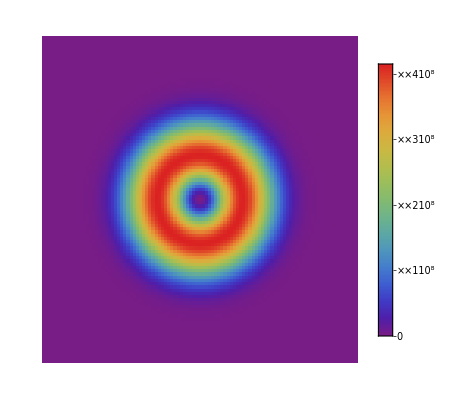

```mathematica
ArrayPlot[Abs[RHO2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
(*Export["/Users/davidlafferty/Projects/vbeams/Mathematica/output/radial_real.csv",Re[RHO2d[[All,All,2,1]]],"CSV"]*)
```

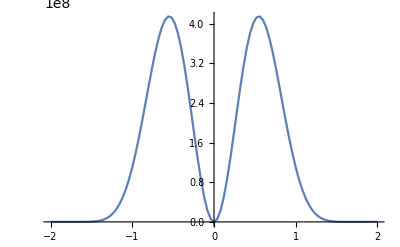

```mathematica
ListLinePlot[Abs[RHO1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Radial phase (for chosen z position)
```

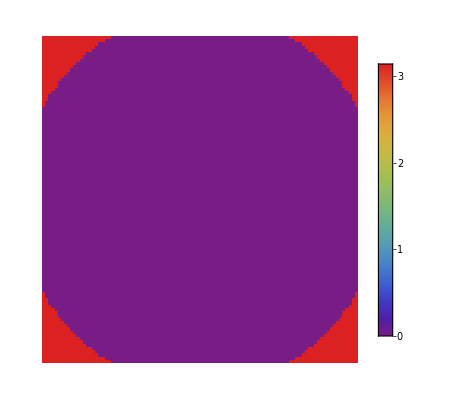

```mathematica
ArrayPlot[Arg[RHO2d[[All,All,51,1]]],PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Radial propagation
```

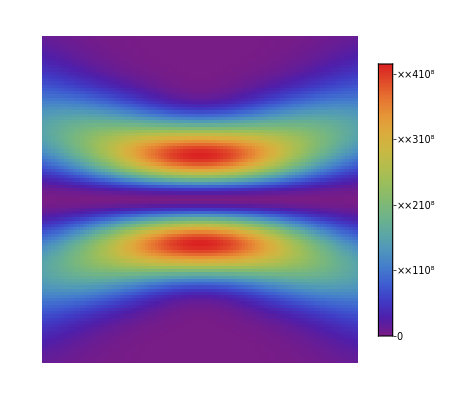

```mathematica
ArrayPlot[Abs[Transpose[RHO1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Longitudinal intensity
```

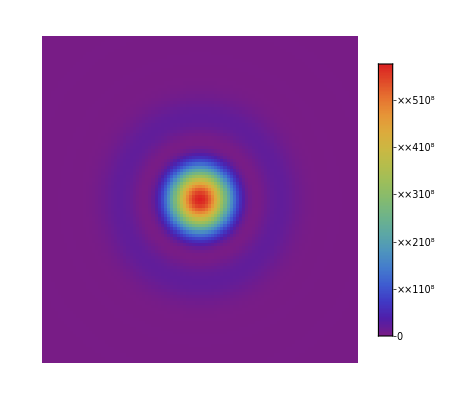

```mathematica
ArrayPlot[Abs[Z2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
(*Export["/Users/davidlafferty/Projects/vbeams/Mathematica/output/axial_imag.csv",Im[Z2d[[All,All,2,1]]],"CSV"]*)
```

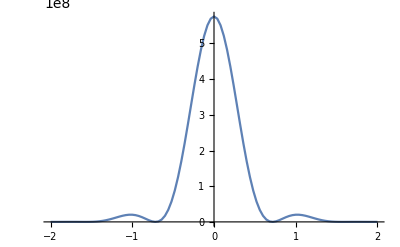

```mathematica
ListLinePlot[Abs[Z1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Longitudinal phase (for chosen z position)
```

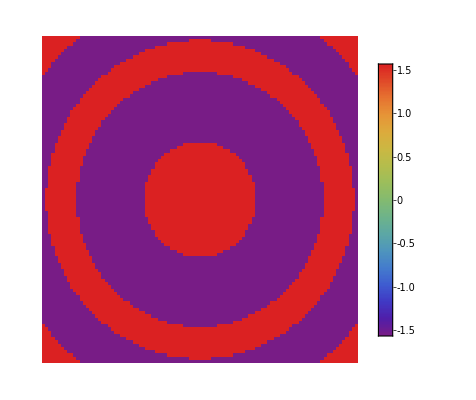

```mathematica
ArrayPlot[Arg[Z2d[[All,All,51,1]]],PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Longitudinal propagation
```

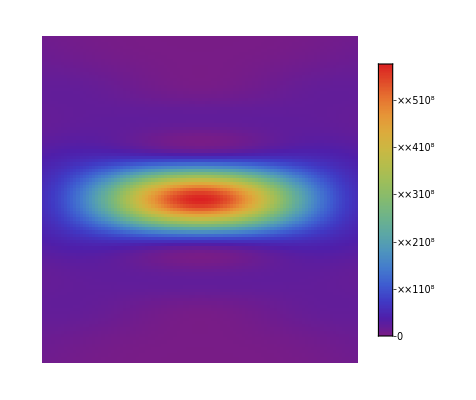

```mathematica
ArrayPlot[Abs[Transpose[Z1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Combined (radial and longitudinal) intensity
```

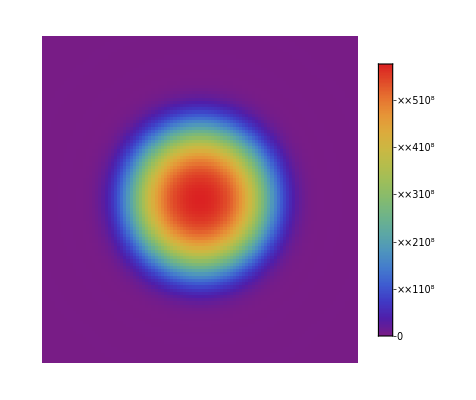

```mathematica
ArrayPlot[Abs[RHO2d[[All,All,51,1]]]^2+Abs[Z2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Export["/Users/davidlafferty/Projects/vbeams/Mathematica/output/zrad_real.csv",Re[RHO2d[[All,All,51,1]]]+Re[Z2d[[All,All,51,1]]],"CSV"]
```

/Users/davidlafferty/Projects/vbeams/Mathematica/output/zrad_real.csv

```mathematica
Export["/Users/davidlafferty/Projects/vbeams/Mathematica/output/zrad_imag.csv",Im[RHO2d[[All,All,51,1]]]+Im[Z2d[[All,All,51,1]]],"CSV"]
```

/Users/davidlafferty/Projects/vbeams/Mathematica/output/zrad_imag.csv

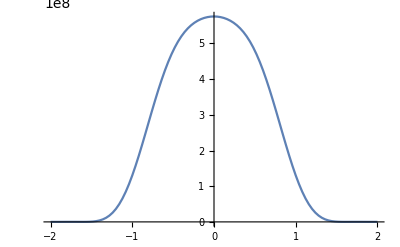

```mathematica
ListLinePlot[Abs[RHO1d[[51,1]]]^2+Abs[Z1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Combined phase
```

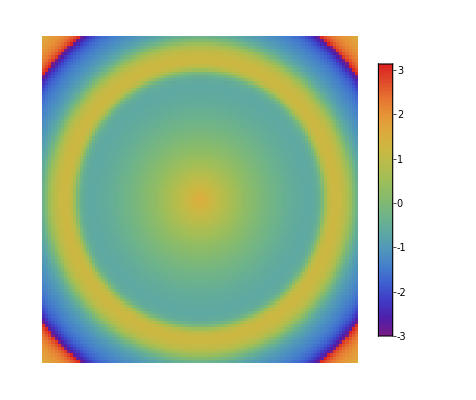

```mathematica
ArrayPlot[Arg[RHO2d[[All,All,51,1]]+Z2d[[All,All,51,1]]],PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Combined propagation
```

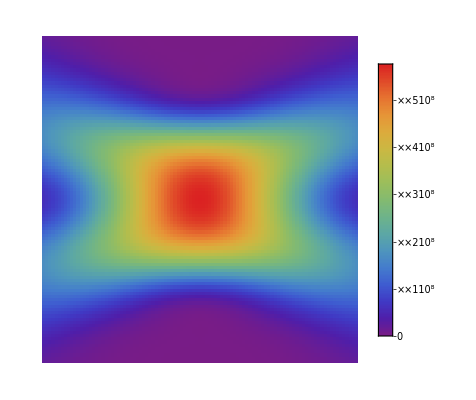

```mathematica
ArrayPlot[Abs[Transpose[RHO1d[[All,1]]]]^2+Abs[Transpose[Z1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Azimuthal intensity
```

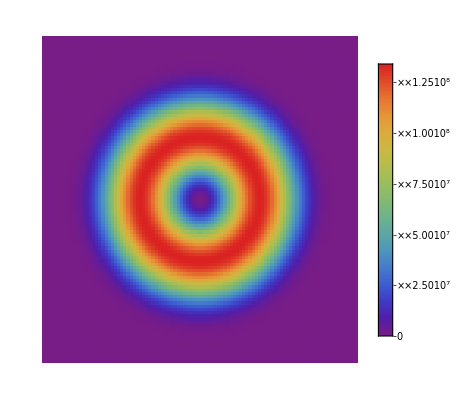

```mathematica
ArrayPlot[Abs[PHI2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
(*Export["/Users/davidlafferty/Projects/vbeams/Mathematica/output/azimuthal_real.csv",Re[PHI2d[[All,All,2,1]]],"CSV"]*)
```

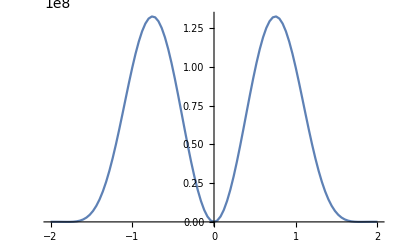

```mathematica
ListLinePlot[Abs[PHI1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Azimuthal phase
```

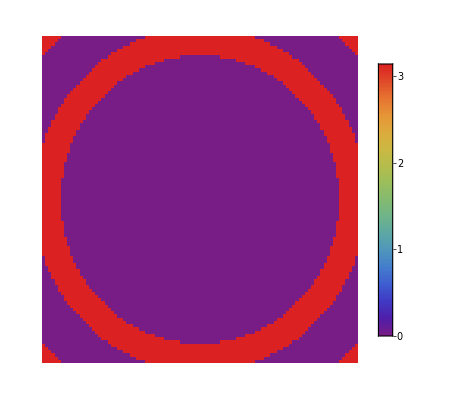

```mathematica
ArrayPlot[Arg[PHI2d[[All,All,51,1]]],PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Azimuthal propagation
```

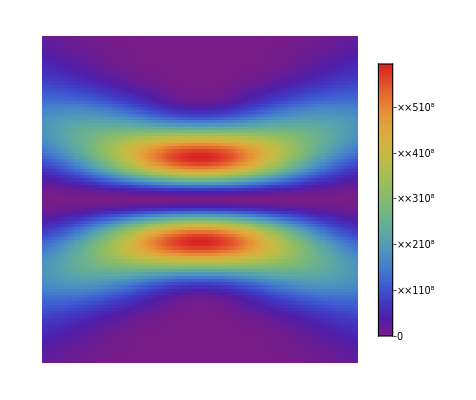

```mathematica
ArrayPlot[Abs[Transpose[PHI1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Azimuthal propagation (with added cosine term)
```

```mathematica
ArrayPlot[Abs[Transpose[PHI1dcos[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

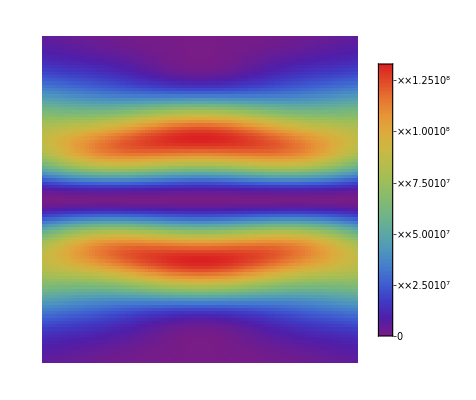

```mathematica
Linear Combinations
```

```mathematica
ϕ=Table[Arg[Complex[y,x]],{x,Range[min λ,max λ,(max-min)/step λ]},{y,Range[min λ,max λ,(max-min)/step λ]}];
```

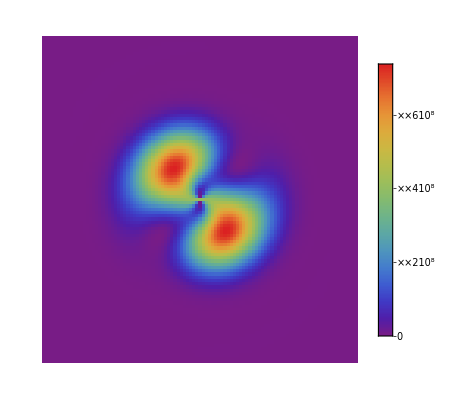

```mathematica
ArrayPlot[1/(√2) Abs[Cos[ϕ]*(RHO2d[[All,All,51,1]]+Z2d[[All,All,51,1]])+Sin[ϕ]*PHI2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```